# MMA Notes

2023.09.04

## Notebook format

Clear all $Context variables:

```mathematica
ClearAll/@(($Context<>"*")//Names);
```

Set the outline box:

```mathematica
SetOptions[EvaluationNotebook[], DockedCells->{Cell[BoxData[ToBoxes[ResourceFunction["NotebookOutlineMenu"][EvaluationNotebook[]]]]]}]
```

## MMA cheat sheet

## Information

?symbol (Show information of that symbol)

??symbol (Show more detailed information of that symbol)

?*symbol* (Show information of that symbol with regex. e.g. ?*Q)

## operator

+ (Plus), - (Subtract), * (Times), / (Divide), ^ (Power), += , -=, *=, /=

> (Greater), != (Unequal), && (And), <= (LessEqual), || (Or), == (Equal, equal of value after evaluation)

=== (SameQ, equal of the whole expression),  =!= (UnsameQ)

## Results

% (the last result)

%% (n % means the output of last n runs), equals %n or Out[n]

## Assignment

lhs = rhs (Set, assign the evaluation result of rhs to lhs instantaneously)

lhs := rhs (SetDelayed, assign the evaluation result of rhs to lhs whenever the lhs is utilized)

## List

{a, b, c,{d,e}} (A list is defined in {})

```mathematica
alist={{a,b},{c,{d,e}}}
```

{{a,b},{c,{d,e}}}

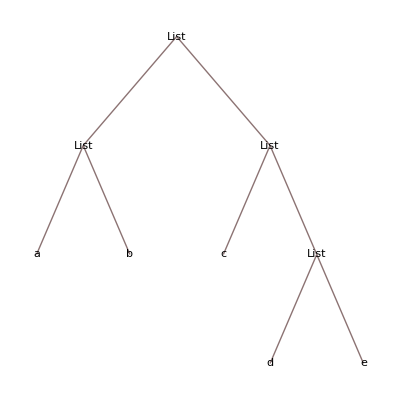

```mathematica
alist//TreeForm
```

Level[list, {level_you_want_to_Part}] (Return the list in the corresponding level. Level 0 means the whole list or the entire expression. Level 1 removes one layer from the top of the tree form.)

```mathematica
Level[alist,{1}]
```

{{a,b},{c,{d,e}}}

```mathematica
Level[alist,{2}]
```

{a,b,c,{d,e}}

Position[list, element] (Return the position of the element in a list.)

```mathematica
Position@@{alist, d}
```

{{2,2,1}}

MapAt[function, list, position] (Map the function on the specified position.)

```mathematica
MapAt[f,alist,{2,2,1}]
```

{{a,b},{c,{f[d],e}}}

MapThread (Map on the columns of the matrix)

```mathematica
MapThread[f,{{a1,a2}, {b1,b2},{c1,c2}}]
```

{f[a1,b1,c1],f[a2,b2,c2]}

Thread (e.g. Thread[f[{a1, b1}, {b1,b2}, c]] outputs {f[a1, b1, c], f[b1,b2,c]}. The Thread works on the column part of a list, and take the scalar as the public argument. )

```mathematica
Thread[f[{a1,b1},{b1,b2},c]]
```

{f[a1,b1,c],f[b1,b2,c]}

```mathematica
Thread[Equal[{1,2,3},{1,2,6}]//Unevaluated]
```

{True,True,False}

Through (e.g. Through[{f,g,h}, {a,b,c}] outputs {f[a,b,c], g[a,b,c], h[a,b,c]}. The Through make functions working on a single argument list.)

```mathematica
Through[{f,g,h}[a,b,c]]
```

{f[a,b,c],g[a,b,c],h[a,b,c]}

MapIndexed (Some functions need take value + index as their arguments.)

```mathematica
MapIndexed[f,{a,b,c}]
```

{f[a,{1}],f[b,{2}],f[c,{3}]}

```mathematica
MapIndexed[f,{{a,b,c},{d,e}}] (* working on level 1 *)
```

{f[{a,b,c},{1}],f[{d,e},{2}]}

```mathematica
MapIndexed[f,{{a,b,c},{d,e}},{2}] (* working on level 2 *)
```

{{f[a,{1,1}],f[b,{1,2}],f[c,{1,3}]},{f[d,{2,1}],f[e,{2,2}]}}

```mathematica
diagQ[m_]:=Module[{},
(* #1 is the element value in 2d matrix, and #2 is the corresponding position *)
MapIndexed[((#1==0)&&Unequal@@#2) || Equal @@ #2 &, m, {2}]//Flatten //And @@# &
];
diagQ[{{1,0},{0,1}}]
```

True

```mathematica
diagQ[{{1,0},{1,1}}]
```

False

```mathematica
Level[{{1,0},{1,1}},{2}]
```

{1,0,1,1}

Nest, NestList, FixedPoint

```mathematica
Nest[1/(1+#)&,x,3]
```

1/(1+1/(1+1/(1+x)))

```mathematica
NestList[1/(1+#)&,x,3]
```

{x,1/(1+x),1/(1+1/(1+x)),1/(1+1/(1+1/(1+x)))}

```mathematica
FixedPoint[(#+2/#)/2 &,1.] (*start with 1, and converge to 1.414*)
```

1.41421

```mathematica
FixedPointList[(#+2/#)/2&,1.]
```

{1.,1.5,1.41667,1.41422,1.41421,1.41421,1.41421}

TableForm[list], MatrixForm[list]

```mathematica
TableForm[{{a,Sqrt[3],c},{d,3,N[Pi]}}]
```

a | √3 | c
d | 3 | 3.14159

```mathematica
MatrixForm[{{a,Sqrt[3],c},{d,3,N[Pi]}}]
```

(a | √3 | c
d | 3 | 3.14159)

[[ ]] (Part)

```mathematica
alist[[1]]
```

{a,b}

list[[3]]  (Part the 3rd element)

```mathematica
alist[[1,2]]
```

b

list[[{3,2}]]  (Part the 3rd and 2nd elements)

```mathematica
alist[[{1,2}]]
```

{{a,b},{c,{d,e}}}

list[[1,2]] (Part the 2nd element in the 1st element)

Range[...] , Array[...], Table[expression, {variable, start, end, step}] (The Table function is the most useful one)

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Range[4,12,2]
```

{4,6,8,10,12}

```mathematica
Array[f,10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
Table[Prime@i,{i,1,10,1}]
```

{2,3,5,7,11,13,17,19,23,29}

Only AppendTo and PrependTo will modify the list itself. All other list functions will not modify the original list.

```mathematica
Length[{a,b,c}]
```

3

```mathematica
Dimensions@ {{a,b,c},{d,e,f}}
```

{2,3}

```mathematica
MemberQ[{a,b,c},d]
```

False

```mathematica
Count[{a,b,c,a},a]
```

2

```mathematica
blist={a,b,c,d,e}
```

{a,b,c,d,e}

```mathematica
Append@@{blist,42}
```

{a,b,c,d,e,42}

```mathematica
Prepend@@{blist,{x,y}}
```

{{x,y},a,b,c,d,e}

```mathematica
Insert[blist,Pi,4]
```

{a,b,c,π,d,e}

```mathematica
blist
```

{a,b,c,d,e}

```mathematica
AppendTo[blist,42];blist
```

{a,b,c,d,e,42}

```mathematica
PrependTo[blist,{x,y}];blist
```

{{x,y},a,b,c,d,e,42}

```mathematica
ReplacePart[blist,new,1]
```

{new,a,b,c,d,e,42}

```mathematica
Take[blist,{2,4}]
```

{a,b,c}

```mathematica
Drop[blist,{2,4}]
```

{{x,y},d,e,42}

## String

The built-in string functions are similar with the built-in string functions. Like StringLength, StringPosition, StringQ, LetterQ, DigitQ, StringMatchQ, StringTake, StringDrop, StringInsert ...

```mathematica
StringJoin["Hello ", "world","!"]
```

Hello world!

```mathematica
"Hello" <> " world"<>"!"
```

Hello world!

```mathematica
a=2;ToExpression["a+b"]
```

2+b

## Function (DownValues, UpValues)

MMA is fundamentally a functional programming language. Functional means that functions and data are indistinguishable: functions can be treated like data and passed between functions. MMA’s kernel is also called the infinite evaluation system. The heuristic evaluation process can be regarded as expression //. {all global rules}. During the evaluation if function overloading occurred, e.g. f[0] vs f[x_Integer] (two UpValues of f), the MMA will always use the more specific rules.

@ (Prefix, e.g. f @ x,  Prefix can only be used for functions with single argument. It is only for saving the [], with no additional semantics. )

/@ (Map, e.g.  f /@ {a,b,c} equals {f[a], f[b], f[c]}. It can also avoid the trouble of defining the Listable attribute for a symbol. )

@@ (Apply, e.g. f @@ {a,b,c} means f[a,b,c]. The Apply means to replace the Head)

pure function. Like Power @@ # &. # (Slot) means formal variable and & terminates the pure function. We can also use #1, #2, ...

//  (Postfix, e.g.  x // f)

x~f~y (Infix)

Note that priority: Prefix > Infix > Postfix. No need to memorize. It is always a good habit to use ().

f[x_,y_] := expr (_ is called Blank)

f[x_,y_] := first line; second line; ... last line is called the compound expression.

Note that modifying function arguments is not permitted in MMA. This restriction exists because when functions are called, all arguments are evaluated and replaced wherever they appear within the function.

Attributes[] show attributes of a function. e.g. Protected

```mathematica
Attributes@Sqrt
```

{Listable,NumericFunction,Protected}

Listable (Listable is an attribute of a function. Virtually all of the built-in numerical functions (e.g. Plus, Sin, Gamma), predictive functions (xxQ, e.g. IntegerQ, PrimeQ) and some of the symbolic functions (e.g. Together, ToExpression) have the Listable attribute. For a function f with Listable attribute,  f[{list}] equals {f[list[[1]]], f[list[[2]]] ...} )

```mathematica
Sqrt[{a,b,c}]
```

{√a,√b,√c}

```mathematica
{a,b,c}^d
```

{a^d,b^d,c^d}

```mathematica
a^{a,b,c}
```

{a^a,a^b,a^c}

```mathematica
greater2[x_]:=x>2;
greater2[{1,2,3}]
```

{1,2,3}>2

```mathematica
greater2/@{1,2,3}
```

{False,False,True}

```mathematica
SetAttributes[greater2, Listable]
greater2[{1,2,3}]
```

{False,False,True}

Clear, ClearAll, Remove (Clear means to clear the Rules (OwnValues, UpValues, DownValues ... ) attached with the symbol. ClearAll means to clear the the Rules, Options, and Attributes attached with the symbol. Remove means to remove the symbol from the symbol table (do not use Remove...Because its mechanism is not very clear. )
e.g. ClearAll/@(($Context<>"*")//Names);      )

Predication in MMA, like *Q functions, is used to predicate if an expression has some attributes.

```mathematica
Select[{a,1.1,Sqrt[3],4.5,5},IntegerQ]
```

{5}

```mathematica
{VectorQ[{a,b,c}],VectorQ[{a,b,{a,b}}]}
```

{True,False}

```mathematica
?*Q
```

Module in MMA, is a function with local variables.

```mathematica
quad[a_,b_,c_:0]:=Module[
{d,e},
d=Sqrt[b^2-4 a c];
e=2 a;
{-b + d, -b-d} / e
];
```

```mathematica
{quad[1,1,1],d,e}
```

{{1/2 (-1+ⅈ √3),1/2 (-1-ⅈ √3)},d,e}

```mathematica
quad[1,1]
```

{0,-1}

Besides Module, the With function can also define local variables. The name in With[{name=expr}, body] is not a variable but a macro like #define in C; it will replace the name anywhere in body to expr, so that the name can not be assigned to another value after the first definition. Advantage: faster than Module.

```mathematica
Clear[quad]; quad[a_,b_,c_:0]:=With[
{d = Sqrt[b^2-4 a c], e = 2 a},
{-b+d,-b-d}/e
]
```

```mathematica
quad[1,0,-16]
```

{4,-4}

## Rules

The evaluation process of MMA is just like expression //. {all global rules}.

type of rule | for evaluation of | example
OwnValues[sym] | sym | sym:=
DownValues[sym] | sym[...] | sym[...]:=
UpValues[sym] | head[...sym...] or head[..._sym...] | head[...sym...]^:= or sym /: head[...sym...]:=
SubValues[sym] | sym[...][...] | sym[...][...]:=...
NValues[sym] | N[sym, precision] or N[sym[...],precision] | N[sym[...],precision]:=...
FormatValues[sym] | format[sym[...]] | Format[sym[...],format]:=

a -> b (form of a Rule)

/. (ReplaceAll[expr, rule])

//. (ReplaceRepeated)

Options[symbol]  (check the options of a symbol (usually a function). The options are shown in the rule format and can usually be modified. The option rule is shown as name -> value and name :> value.)

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
Cases[{f[x],f[x,a->b],f[x,a:> b, c->d],f[x,{a->b,c->d},e->f]},f[arg1_,opt___?OptionQ]->{opt}]
```

{{},{a→b},{a:>b,c→d},{{a→b,c→d},e→f}}

```mathematica
f[x_,a->b]:=x;
```

```mathematica
f[x,a->b]
```

x

SetOptions[symbol, option]

=. (Unset a rule. e.g. f[x_]=. means clear the DownValues of f, but the DownValues of f[x_Integer] will remain in DownValues[f]. f =. means to clear OwnValues of f.)

pattern:value, pattern with default value. e.g. x_:2

_. means a pattern with default value 0 and can input nothing. e.g. f[x_, y_.]  (Have to use Default[f] = 0 first!!!)

__ (BlankSequence. One or more patterns. Different patterns are separated using , )

___ (BlankNullSequence. Zero or more patterns.  Different patterns are separated using ,  )

_head (pattern constraints. Only match those patterns whose Head is head)

```mathematica
factorial[n_Integer]:=Product[i,{i,n}];
factorial[4]
factorial[3.5]
```

24

factorial[3.5]

```mathematica
squareAnyNumber[n_?IntegerQ|n_Real|n_Rational|n_Complex|(n_ /; VectorQ@n)]:=n^2;
```

```mathematica
squareAnyNumber/@{3,4.5,2/3,3+4 I, {1,2,3},x}
```

{9,20.25,4/9,-7+24 ⅈ,{1,4,9},squareAnyNumber[x]}

_?testFunctionReturnTrueOrFalse (pattern constraints. Only match those patterns that make test function(symbol) return True)

pattern /; testFunctionReturnTrueOrFalse (Condition. Only match those patterns that make test function return True )

name:pattern (Assign the alias name to the pattern, similar to n_, with the advantage that the subsequent pattern can be sufficiently complex.)

pattern.. (pattern repeated 1 or more times)

pattern... (pattern repeated 0 or more times)

pattern1 | pattern2 (match pattern1 or pattern2)

^:= (UpSetDelayed, set UpValues of arguments in functions)

/: ... :=  (TagSetDelayed. A better way to set UpValues of arguments in functions)

## Everything is an expression

In Mathematica, everything is an expression. 
Every expression is a combination of normal expressions. 
A normal expression can be constructed using 3 parts: 1. atoms (symbol, number, string),  2. square brackets [],  3. commas , . 
The [] and commas can be regarded as the special symbols.

In summary, in MMA, everything is an expression, and every  expression is a combination of symbols.

### atoms

symbol

The Symbol in MMA, is a sequence of letters, digits and character $.

All the system-defined atoms start with capital letters and $. (e.g. Plus, D, FullForm, $Version, $MachinePrecision)

The *, + , and / are still the symbols (Times, and Plus) in MMA.

Every expression has a Head, and the Head is called the type of the expression.

```mathematica
Head[Plus]
```

Symbol

```mathematica
Head[$MachinePrecision]
```

Real

```mathematica
Head/@{3,3/2,3+2*I,{3,2},a}
```

{Integer,Rational,Complex,List,Integer}

number

The numbers in MMA have 4 types: Integer, Real, Rational (integer1 / integer2), Complex (a+b I)

```mathematica
Head[1.]
```

Real

```mathematica
Head[1/2]
```

Rational

```mathematica
Head[1+2 I]
```

Complex

Note that the Head of an expression is the top layer of its tree form,which is used for the evaluation process.

string

The string in MMA is a sequence of characters enclosed by double quotes (“sth.”).

The \” stands for the single “.

```mathematica
Head["\"hello world\""]
```

String

```mathematica
"\"hello world\""
```

"hello world"

### Forms

The FullForm and TreeForm expression show the expressions in MMA’s view. The evaluation process of a normal expression is from tree’s bottom to its top.

```mathematica
FullForm[4 * a^2]
```

Times[4,Power[a,2]]

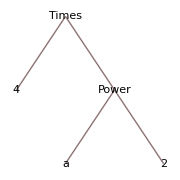

```mathematica
TreeForm[4*a^2]
```

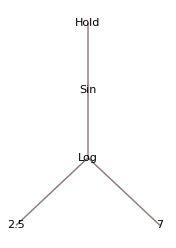

```mathematica
TreeForm[Hold[Sin[Log[2.5,7]]]]
```

## Evaluation process of an expression

The evaluation process in MMA involves the iterative replacement of rules associated with their corresponding symbols until no further rule replacement are possible.

Types of rules

There is 6 types of rules. The symbol with rules is called the rule’s tag.

type of rule | for evaluation of | example
OwnValues[sym] | sym | sym:=
DownValues[sym] | sym[...] | sym[...]:=
UpValues[sym] | head[...sym...] or head[..._sym...] | head[...sym...]^:= or sym /: head[...sym...]:=
SubValues[sym] | sym[...][...] | sym[...][...]:=...
NValues[sym] | N[sym, precision] or N[sym[...],precision] | N[sym[...],precision]:=...
FormatValues[sym] | format[sym[...]] | Format[sym[...],format]:=

In the case of a symbol with OwnValues, the symbol itself will be replaced during evaluation.

```mathematica
a:=b+c
```

```mathematica
OwnValues[a]
```

{HoldPattern[a]:>b+c}

```mathematica
Head[a]
```

Plus